# Markov chain baseline for Reinforcement Learning.

### Baseline 1: Optimization, Space of image (zero learning)

Optimization procedure

In the space of the image parameters (5 - 6)

Local optimization

Markov chain evolution

Make a small change of the parameters

Compute over a certain time (0.2s  - 1s) the average happiness

If better, accept

If worse, reject (or accept according to a probability)

Implementation:

```mathematica
trainedConvNet = Import["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/shallow/2017-06-29T14:37:34_1_07_2251_8.18e-1_1.02e+0.wlnet"]
```

NetChain[]

### Define all variables that can be used to manipulate animation

```mathematica
r = 0.5;
t = 0.8;
s = 0.5;
a = 0;
b = 0.6;
c =0;
ey = 0.16;
er = 0;
```

```mathematica
ParametersStruct = {
{.5,0,1.1},
{.8,0,Pi},
{.1,0,.5},
{0,-1,1},
{.6,-1.2,1.2},
{0,-2,2},
{.16,.05,.3},
{0,-1,1}
};
```

```mathematica
animation =   Dynamic[Graphics[{Yellow,Disk[{0,0},1],Black,MapIndexed[{Disk[#,s],Thickness[.008],Line[{#+{-.13,ey-er (-1)^First[#2]},#+{.13,ey+er(-1)^First[#2]}}]}&,{r {Sin[t],Cos[t]},r{-Sin[t],Cos[t]}}],Thickness[.02],First[Plot[-.35+a x+ b x^2+c x^3,{x,-.4,.4},PlotStyle->Black]]},PlotRange->All,ImageSize->{400,400}]
];
```

```mathematica
nFrames = 10;
step = 1;
currentHappines = 0.;
previousHappines = 0.; 
happinessesList= {{r,t ,s,a ,b,c ,ey ,er, currentHappines}};
ResetParameters[];

Dynamic[
parameter = SelectParameter[];
previousParamValue = KeepPreviousParameterValue[parameter];
update =  CalculateParameterUpdate[parameter,step];
UpdateParmeter[parameter,update];

frame =0;
currentHappines= 0.;
Column[{ animation,
While[frame < nFrames,
image=CurrentImage[];
greyFace= ExtractFaceFromImage[image];
currentHappines += PredictHappinessProbability[greyFace];
frame++;
];
currentHappines/=nFrames;image,greyFace, currentHappines, 
If[currentHappines>previousHappines ,previousHappines =  currentHappines, ReloadParameterValue[parameter, previousParamValue]];
happinessesList= Join [happinessesList,{{r,t ,s,a ,b,c ,ey ,er, currentHappines}}];}
]

]
```

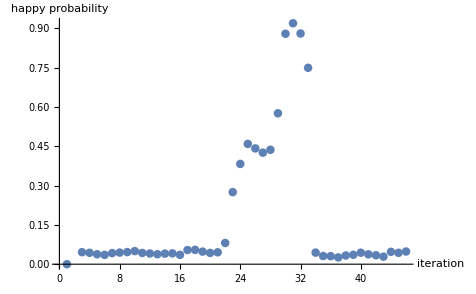

```mathematica
ListPlot[happinessesList[[All,9]],AxesLabel->{"iteration","happy probability"}]
```